```mathematica
nodes := Range[1980, 2000, 2]
```

```mathematica
values := { 338.7, 341.1, 344.4, 347.2, 351.5, 354.2, 356.4, 358.9, 362.6, 366.6, 369.4 }
```

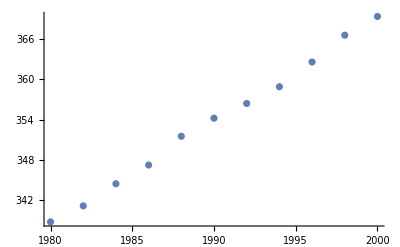

```mathematica
ListPlot[{Table[{nodes[[i]], values[[i]]}, {i, 1, Length[values]}]}]
```

```mathematica
f[x_] := b*x + c
```

```mathematica
sum = Sum[{(f[nodes[[i]]] - values[[i]])^2},{i , 1, Length[nodes]}]
```

{(-338.7+1980 b+c)^2+(-341.1+1982 b+c)^2+(-344.4+1984 b+c)^2+(-347.2+1986 b+c)^2+(-351.5+1988 b+c)^2+(-354.2+1990 b+c)^2+(-356.4+1992 b+c)^2+(-358.9+1994 b+c)^2+(-362.6+1996 b+c)^2+(-366.6+1998 b+c)^2+(-369.4+2000 b+c)^2}

```mathematica
Solve[{D[sum, b] == 0, D[sum, c] ==0}, {b, c}]
```

{{b→1.53818,c→-2707.25}}